## Computational Model

```mathematica
ResourceFunction["WolframRicciCurvatureTensor"]
```

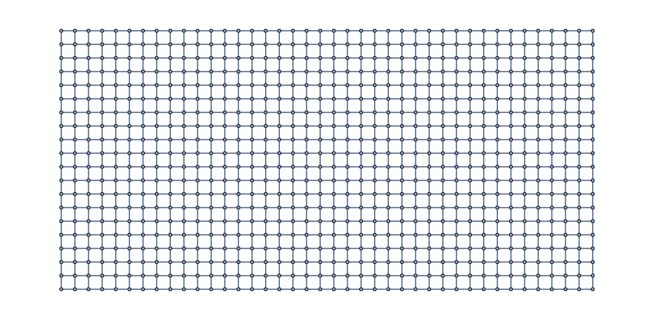

```mathematica
gridGraph = GridGraph[{20, 40}]
```

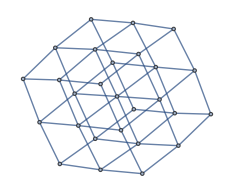

```mathematica
gridGraph3D = GridGraph[{3,3,3}]
```

```mathematica
Table[GridGraph[{i,j}, PlotLabel->Subscript[G, i,j], PlotTheme->"Monochrome"], {i, 3, 6}, {j, 2, 8}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

-Graphics-

```mathematica
Image[RandomReal[1, {100, 100}]]
```

-Graphics-

```mathematica
ResourceFunction["MultiwayTuringMachine"]
```

```mathematica
[{2504, 3506}, {{1, 1, 0}, {0, 1, 0}},4, "StatesGraph", VertexSize -> 1]
```

-Graphics-

```mathematica
recFxnTime[x_] := (((1+Sqrt[5])/2)^x)
```

```mathematica
timeComplex[n_] := Plot[{recFxnTime[x], x}, {x, 0, n},PlotRange->{{0, 10},{0,100}},PlotStyle -> {Thickness[0.02], Thickness[0.01]}, PlotLabel->  "time complexity",AxesLabel -> {n, time},PlotLegends->Placed[LineLegend[{"recursive", "iterative"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.25,0.5},{0.25,0.1}}],ImageSize->{200,200}]
```

```mathematica
spaceComplex[n_] := Plot[{x, x}, {x, 0, n},PlotRange->{{0, 10},{0,20}},PlotStyle -> {Thickness[0.02], Thickness[0.01]}, PlotLabel->  "space complexity",AxesLabel -> {n, space}, PlotLegends->Placed[LineLegend[{"recursive", "iterative"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.25,0.5},{0.25,0.1}}],ImageSize->{200,200}]
```

```mathematica
itTree[n_]:=Module[ {itTreeArray = {}, n0 = n} ,
					For[i=2,i<=n0,i++,AppendTo[itTreeArray, i-2 -> i];  AppendTo[itTreeArray,i-1 -> i]];
					TreePlot[itTreeArray,Right,  VertexLabeling->True, DirectedEdges->True, VertexRenderingFunction->(Inset[#2,#1]&), PlotStyle->Directive[PointSize[Medium]],ImageSize->{200,200}]
					]
```

```mathematica
f[___,0]:={};
f[___,1]:={};
f[m___,p_]:={{m,p}->{m,p,p-1},{m,p}->{m,p,p-2},f[m,p,p-1],f[m,p,p-2]}
	j[n_] := f[n]//Flatten
```

```mathematica
recTree[n_] :=TreePlot[j[n],Top,{n},DirectedEdges->True,VertexRenderingFunction->(Inset[Row[{Last[#2]}],#1]&), PlotRangePadding->0, PlotStyle->Directive[PointSize[Medium]], AspectRatio->0.7,ImageSize->{200,200}]
```

```mathematica
Manipulate[GraphicsGrid[{{timeComplex[n], spaceComplex[n]}, {Show[Graphics[itTree[n]], PlotLabel -> "iterative tree"], Show[Graphics[recTree[n]], PlotLabel -> "recursive tree"]}},  Alignment ->{ Center, Top},Frame -> All], {{n, 2, "Fibonacci number"}, 2, 10, 1,Appearance->"Labeled"},ControlPlacement->Top, SaveDefinitions->True]
```

```mathematica
Manipulate[Pane[TreeForm[intermediateSteps[[step]],VertexLabeling->labelings]/.Plus->"+"/.Times->"x",{450,450},Alignment->{Center,Center}],{{step,Floor[Length[intermediateSteps]/2]},2,Length[intermediateSteps],1},{{labelings,False,"label nodes"},{True,False}},Initialization:>{Clear[f];f[1]=1;f[2]=1;
intermediateSteps=NestWhileList[#/.f[n_Integer]->(f[1 + n - 2*f[-1 + n]] + f[f[-1 + n]])&,f[8],!IntegerQ[#]&,1];}]
```

## Quantum Computing

```mathematica
x[t_]:=Cos[t]
```

```mathematica
snapshots = Table[x[π RandomReal[j]],{j, 10000}]
```

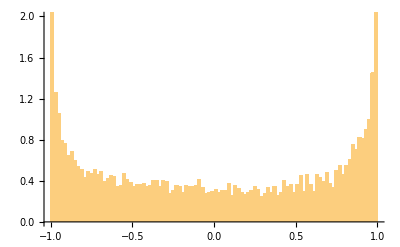

```mathematica
Histogram[snapshots, 100, "PDF", PlotRange->{0,2}]
```

```mathematica
True && False
```

False

```mathematica
AstroPosition[Entity["Planet","Mars"],"Equatorial"]
```

AstroPosition[…]

```mathematica
%["Data"]
```

{71.7773,24.9263,0.564479}

```mathematica
GeoPosition[Here]
```

GeoPosition[{34.05,-118.24}]

```mathematica
MoonPhase[]
```

0.6125

```mathematica
Entity["City",{"Hermosillo","Sonora","Mexico"}]
```

```mathematica
AstroGraphics[Entity["Star","Sirius"]]
```

-Graphics-

```mathematica
Expand[Sum[i x^i, {i,15}]]
```

x+2 x^2+3 x^3+4 x^4+5 x^5+6 x^6+7 x^7+8 x^8+9 x^9+10 x^10+11 x^11+12 x^12+13 x^13+14 x^14+15 x^15

```mathematica
Factor[%]
```

x (1+2 x+3 x^2+4 x^3+5 x^4+6 x^5+7 x^6+8 x^7+9 x^8+10 x^9+11 x^10+12 x^11+13 x^12+14 x^13+15 x^14)

```mathematica
PositionLargest[{1,2,4,0,7}]
```

{5}

```mathematica
Graph[{1->2,2->3,1->4, 2->3, 3-> 5}]
```

-Graphics-

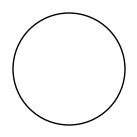

```mathematica
Graphics[Circle[]]
```

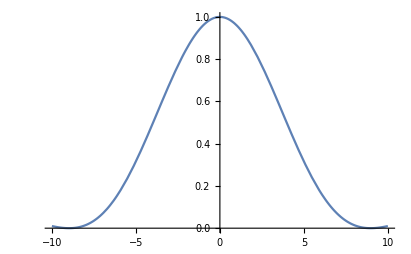

```mathematica
Plot[(ChebyshevU[0,Cos[x]]*Sinc[0.35*x])^2,{x,-10,10}]
```

```mathematica
$GeoLocation
```

GeoPosition[{1.3,103.86}]

```mathematica
$GeoLocation
```

GeoPosition[{22.29,114.15}]

```mathematica
GeoGraphics[GeoCircle[Here,Quantity[15,"Kilometers"]]]
```

-Graphics-

```mathematica
$GeoLocationCity
```

Putian

```mathematica
CityData[Entity["City",{"Putian","Fujian","China"}],"Population"]
```

2860000 people

plot 1/sin x cos y

WolframAlphaQueryResults

```mathematica
f[x_,y_]:=1/(Sin[x] Cos[y])
Plot3D[f[x,y],{x,-π,π},{y,-π,π},AxesLabel->{"x","y","z"},PlotRange->Full]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t] Cos[t]^2,Sin[t] Sin[t]^2,Cos[t]^3},{t,0,2 Pi},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotStyle->Red,Lighting->"Accent"]
```

-Graphics3D-